```mathematica
ClearAll["Global`*"];
Remove["Global`*"];

Off[RuleDelayed::rhs]
PrependTo[$Path,"/home/sounak/Codes2/"];
<<psgSolver`
```

```mathematica
SGSet;
```

```mathematica
initPSGSolver[];
rels=MatrixRelations[SGSet];
rels=decomposeGtoFM[rels];

rels2=phaseSolverIterate[rels];
Column[%]
```

(M^α)_gc·(M^α)_gc·(M^α)_gc=η_4
(M^α)_ga·(M^δ)_ga=η_5 η_7
(M^α)_gb·(M^γ)_gb=η_6 η_7
((M^δ)_ga)^-1·((M^β)_gc)^-1·((M^δ)_gb)^-1·(M^δ)_ga·(M^α)_gc=η_8 η_14 η_16
((M^γ)_gb)^-1·((M^β)_ga)^-1·(M^β)_gb·(M^δ)_ga=η_7 η_17
((M^α)_gc)^-1·((M^γ)_gb)^-1·(M^γ)_ga·(M^β)_gb·(M^δ)_gc·(M^γ)_gb=η_7 η_13 η_18
(M^β)_gc·(M^δ)_gc·(M^γ)_gc=η_4
(M^β)_ga·(M^γ)_ga=η_5 η_7 η_8
(M^β)_gb·(M^δ)_gb=η_6
((M^γ)_ga)^-1·((M^δ)_gc)^-1·((M^β)_gb)^-1·(M^β)_ga·(M^γ)_gc=η_7 η_8 η_16
((M^δ)_gb)^-1·((M^α)_ga)^-1·(M^α)_gb·(M^γ)_ga=η_7 η_17
((M^γ)_gc)^-1·((M^α)_gb)^-1·(M^α)_ga·(M^δ)_gb·(M^β)_gc·(M^δ)_gb=η_14 η_18
(M^γ)_gc·(M^β)_gc·(M^δ)_gc=η_4
(M^γ)_ga·(M^β)_ga=η_5
(M^γ)_gb·(M^α)_gb=η_6 η_8
((M^β)_ga)^-1·((M^γ)_gc)^-1·((M^α)_gb)^-1·(M^α)_ga·(M^δ)_gc=η_7 η_13 η_14 η_16
((M^α)_gb)^-1·((M^δ)_ga)^-1·(M^δ)_gb·(M^β)_ga=η_7 η_17
((M^δ)_gc)^-1·((M^β)_gb)^-1·(M^β)_ga·(M^γ)_gb·(M^α)_gc·(M^α)_gb=η_8 η_13 η_14 η_18
(M^δ)_gc·(M^γ)_gc·(M^β)_gc=η_4
(M^δ)_ga·(M^α)_ga=η_5 η_8
(M^δ)_gb·(M^β)_gb=η_6 η_7 η_8
((M^α)_ga)^-1·((M^α)_gc)^-1·((M^γ)_gb)^-1·(M^γ)_ga·(M^β)_gc=η_13 η_16
((M^β)_gb)^-1·((M^γ)_ga)^-1·(M^γ)_gb·(M^α)_ga=η_7 η_17
((M^β)_gc)^-1·((M^δ)_gb)^-1·(M^δ)_ga·(M^α)_gb·(M^γ)_gc·(M^β)_gb=η_7 η_8 η_18

```mathematica
getMSubstitutor[HoldPattern[Equation[CenterDot[SU2[M[A_][s_]],y__],rhs_]]]/;FreeQ[List[y],M[A][s]] := Module[{subRule},
subRule=SU2[M[A][s]]-> rhs matrixInvert[CenterDot[y]];
MAssoc[{A,s }]=subRule;
subRule];

getMSubstitutor[HoldPattern[Equation[CenterDot[SU2[Inv[M[A_][s_]]],y__],rhs_]]]/;FreeQ[List[y],M[A][s]] := 
Module[{subRule},
subRule=SU2[M[A][s]]-> rhs^-1 matrixInvert[CenterDot[y]];
MAssoc[{A,s }]=subRule;
subRule];
getMSubstitutor [eq_Equation]=Nothing;
updateMAssoc[A_,s_,subRule_]:=
Module[{newRHS,oldRule},
oldRule=MAssoc[{A,s}];
newRHS=oldRule[[2]]//.{subRule};
MAssoc[{A,s}]=Rule[oldRule[[1]],newRHS];
]
```

```mathematica
substM[eqSet_,eqno_]:=Module[{eq,subRule,newEqSet},
eq= eqSet[[eqno]];
subRule= getMSubstitutor[eq];
If[Not[MatchQ[subRule,Nothing]],
(newEqSet=eqSet//.SubstFormInvM//.{subRule}//.DispFormInvM;
(updateMAssoc[{#1,#2},subRule]&)@@@ Distribute[{symGenSet,slatList},List];
newEqSet),
eqSet
]];
performMSubstitutions[eqSet_]:= Fold[substM,eqSet,Range[1,Length[eqSet]]];
```

```mathematica
CancelInverses[HoldPattern[Equation[CenterDot[SU2[x_],y___,SU2[Inv[x_]]],rhs_]]]:=Equation[CenterDot[y],rhs];
CancelInverses[HoldPattern[Equation[CenterDot[SU2[Inv[x_]],y___,SU2[x_]],rhs_]]]:=Equation[CenterDot[y],rhs];
CancelInverses[x_]=x;
```

```mathematica
initPSGSolver[];
rels=MatrixRelations[SGSet];
iggRules=setIGGrules[rels];
rels=rels//.iggRules;
rels=decomposeGtoFM[rels];
rels2=phaseSolverIterate[rels];
rels3=performMSubstitutions[rels2]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
rels3=performMSubstitutions[rels3]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
rels3=performMSubstitutions[rels3]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
rels3=performMSubstitutions[rels3]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
rels3=performMSubstitutions[rels3]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
rels3=performMSubstitutions[rels3]//z2Simplify//DeleteTrivialEquations;
rels3=reduceEtas[rels3];
rels3=CancelInverses[#]&/@rels3;
Column[%]
MAssoc
Values[FAssoc]
```

(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga=η_7 η_17
(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga=1
((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1=1
((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga=η_7 η_17
((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga=1
((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1=1
((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1=η_7
(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga=1
(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1·(M^δ)_ga·(M^γ)_ga·((M^δ)_gb)^-1=η_17
(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1=η_7

<|{Tx,α}→(M^α)_Tx→τ0,{Tx,β}→(M^β)_Tx→τ0,{Tx,γ}→(M^γ)_Tx→τ0,{Tx,δ}→(M^δ)_Tx→τ0,{Ty,α}→(M^α)_Ty→τ0,{Ty,β}→(M^β)_Ty→τ0,{Ty,γ}→(M^γ)_Ty→τ0,{Ty,δ}→(M^δ)_Ty→τ0,{Tz,α}→(M^α)_Tz→τ0,{Tz,β}→(M^β)_Tz→τ0,{Tz,γ}→(M^γ)_Tz→τ0,{Tz,δ}→(M^δ)_Tz→τ0,{ga,α}→(M^α)_ga→((M^δ)_ga)^-1 η_7,{ga,β}→(M^β)_ga→((M^γ)_ga)^-1,{ga,γ}→Null,{ga,δ}→Null,{gb,α}→(M^α)_gb→((M^γ)_gb)^-1 η_7,{gb,β}→(M^β)_gb→((M^δ)_gb)^-1,{gb,γ}→(M^γ)_gb→((M^δ)_ga)^-1·((M^β)_gb)^-1·(M^β)_ga η_7 η_17,{gb,δ}→Null,{gc,α}→(M^α)_gc→((M^β)_ga)^-1·(M^β)_gb·(M^δ)_ga·((M^δ)_gc)^-1·((M^β)_gb)^-1·((M^γ)_ga)^-1·((M^δ)_ga)^-1·((M^β)_gb)^-1·(M^β)_ga η_7,{gc,β}→(M^β)_gc→((M^γ)_gc)^-1·((M^δ)_gc)^-1,{gc,γ}→(M^γ)_gc→(M^γ)_ga η_7,{gc,δ}→(M^δ)_gc→(M^δ)_gb·((M^γ)_gc)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_gc)^-1 η_17,{T,α}→Null,{T,β}→Null,{T,γ}→Null,{T,δ}→Null|>

{(F^α)_Tx[x_,y_,z_]→1,(F^β)_Tx[x_,y_,z_]→1,(F^γ)_Tx[x_,y_,z_]→1,(F^δ)_Tx[x_,y_,z_]→1,(F^α)_Ty[x_,y_,z_]→1,(F^β)_Ty[x_,y_,z_]→1,(F^γ)_Ty[x_,y_,z_]→1,(F^δ)_Ty[x_,y_,z_]→1,(F^α)_Tz[x_,y_,z_]→1,(F^β)_Tz[x_,y_,z_]→1,(F^γ)_Tz[x_,y_,z_]→1,(F^δ)_Tz[x_,y_,z_]→1,(F^α)_ga[x_,y_,z_]→η_7^(x+y),(F^β)_ga[x_,y_,z_]→η_7^(x+y),(F^γ)_ga[x_,y_,z_]→η_7^(x+y),(F^δ)_ga[x_,y_,z_]→η_7^(x+y),(F^α)_gb[x_,y_,z_]→η_7^(x+z),(F^β)_gb[x_,y_,z_]→η_7^(x+z),(F^γ)_gb[x_,y_,z_]→η_7^(x+z),(F^δ)_gb[x_,y_,z_]→η_7^(x+z),(F^α)_gc[x_,y_,z_]→η_7^(x+z),(F^β)_gc[x_,y_,z_]→η_7^(x+z),(F^γ)_gc[x_,y_,z_]→η_7^(x+z),(F^δ)_gc[x_,y_,z_]→η_7^(x+z),Null,Null,Null,Null}

```mathematica
getMSubstitutor[rels3[[2]]]
```

(M^γ)_gc→(M^γ)_ga η_7

```mathematica
MAssoc
```

<|{Tx,α}→(M^α)_Tx→τ0,{Tx,β}→(M^β)_Tx→τ0,{Tx,γ}→(M^γ)_Tx→τ0,{Tx,δ}→(M^δ)_Tx→τ0,{Ty,α}→(M^α)_Ty→τ0,{Ty,β}→(M^β)_Ty→τ0,{Ty,γ}→(M^γ)_Ty→τ0,{Ty,δ}→(M^δ)_Ty→τ0,{Tz,α}→(M^α)_Tz→τ0,{Tz,β}→(M^β)_Tz→τ0,{Tz,γ}→(M^γ)_Tz→τ0,{Tz,δ}→(M^δ)_Tz→τ0,{ga,α}→(M^α)_ga→((M^δ)_ga)^-1 η_7,{ga,β}→(M^β)_ga→((M^γ)_ga)^-1,{ga,γ}→Null,{ga,δ}→Null,{gb,α}→(M^α)_gb→((M^γ)_gb)^-1 η_7,{gb,β}→(M^β)_gb→((M^δ)_gb)^-1,{gb,γ}→(M^γ)_gb→((M^δ)_ga)^-1·((M^β)_gb)^-1·(M^β)_ga η_7 η_17,{gb,δ}→Null,{gc,α}→(M^α)_gc→((M^β)_ga)^-1·(M^β)_gb·(M^δ)_ga·((M^δ)_gc)^-1·((M^β)_gb)^-1·((M^γ)_ga)^-1·((M^δ)_ga)^-1·((M^β)_gb)^-1·(M^β)_ga η_7,{gc,β}→(M^β)_gc→((M^γ)_gc)^-1·((M^δ)_gc)^-1,{gc,γ}→(M^γ)_gc→(M^γ)_ga η_7,{gc,δ}→(M^δ)_gc→(M^δ)_gb·((M^γ)_gc)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_ga)^-1·((M^δ)_ga)^-1·(M^δ)_gb·((M^γ)_gc)^-1 η_17,{T,α}→Null,{T,β}→Null,{T,γ}→Null,{T,δ}→Null|>

```mathematica
x=Nothing
```

Nothing

```mathematica
x
```

Nothing

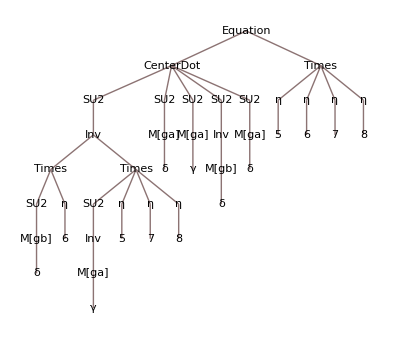

```mathematica
rels3[[3]]//TreeForm
```

```mathematica
rels3[[4]]
```

(SU2_(M[ga][δ]))^-1·((SU2_(M[gc][γ]))^-1·(SU2_(M[gc][δ]))^-1 η_4)^-1·(1/η_5 SU2_(M[ga][δ])·(SU2_(M[gb][γ]))^-1·((SU2_(M[gc][δ]))^-1·SU2_(M[ga][δ])·(SU2_(M[gb][γ]))^-1·SU2_(M[gc][γ]) η_6 η_7^2 η_8 η_13 η_14 η_16) η_6 η_17)^-1·(M^δ)_ga·(M^α)_gc=η_8 η_14 η_16